## Yeast Diffusion Modelling

This program calculates diffusion on a curved surface, a surface of revoution. It is assumed the initial distribution is symmetric about the axis, and we take it to be a step function (1 in some region, 0 elsewhere). 

The step function is a smooth version (using the tanh function), both realistic and easy to deal with numerically.

The shape of the surface can be arbitrary, but for starters we consider overlapping spheres.
The varaible x is length along the axis of revolution. The bigger sphere is centres about x=0.
The smaller sphere intersect the big one at a positive value of x that we call x0num

We have done this calculation with the small sphere having more than one hemisphere. One can also do the less than one hemisphere case (but not done here)

The diffussion equation is:

1/D ∂_t u(t,x,ϕ) = 1/(f √(1 + (f')^2)) ∂_x f/(√(1+(f')^2))∂_x u(t,x,ϕ) + 1/f^2 ∂_ϕ^2 u(t,x,ϕ)
  
  Here f=f(x) is the function that defines the surface of revolution. f' is its derivative.  It has to vanish at its enddoints, f(xmin)=0=f(xmax)
  
  D is the difusion constant. The results below are given with a time coordinate rescaled, so time is in units of D. The solution is assumed to be axisymmetric, so u does not depend on the azimuthaal angle ϕ.

### Preliminaries

#### Initial data

```mathematica
(*rMnum = radius of mother cell*)
(*rRnum = ratio of mother to daughter cell radii*)
(*x0num = bud neck location, where mother & daughter cells intersect*)
(*xfnum = right-most edge of bud*)

rMnum=2.5000000;
rRnum= 2.1000000;
rDnum = rMnum/rRnum;

x0num=2.4000000;
xfnum = x0num + rDnum + Sqrt[x0num^2 + rDnum^2 - rMnum^2];

Print[rMnum^2(1/rRnum^2-1)+x0num^2, " must be positive"]
```

0.927234 must be positive

```mathematica
rDnum
```

1.19048

```mathematica
x0num
```

2.4

Define the circles that characterize the spheres :

```mathematica
fm[x_]=Sqrt[rMnum^2-x^2];
fd[x_]=Sqrt[rDnum^2-(x-x0num-Sqrt[x0num^2+rDnum^2-rMnum^2])^2];
```

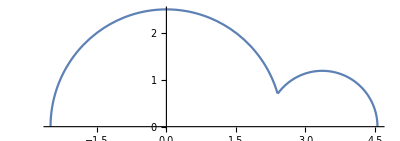

```mathematica
Plot[Piecewise[{{fm[x],x<x0num},{fd[x],x>=x0num}}],{x,-rMnum,xfnum},AspectRatio->rMnum/(rMnum+xfnum)]
```

#### Coefficients of the Diffusion Equation & Initial Conditions

```mathematica
diff[x_]:=Piecewise[{{1,x<x0num},{0.3,x0num≤ x≤ x0num+0.3}},1]
```

```mathematica
diff[x_]:=1
```

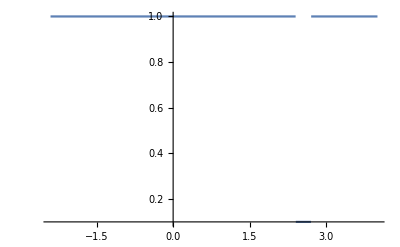

```mathematica
Plot[diff[x],{x,-2.4,4}]
```

```mathematica
cm[x_]=1/(1+D[fm[x],x]^2)//Simplify;
cd[x_]=1/(1+D[fd[x],x]^2)//Simplify;
cddiff[x_]=diff[x]/(1+D[fd[x],x]^2)//Simplify

dm[x_]=1/(fm[x]Sqrt[1+D[fm[x],x]^2])D[fm[x]/Sqrt[1+D[fm[x],x]^2],x]//FullSimplify;
dd[x_]=1/(fd[x]Sqrt[1+D[fd[x],x]^2])D[fd[x]/Sqrt[1+D[fd[x],x]^2],x]//FullSimplify;
ddiff[x_]=1/(fd[x]Sqrt[1+D[fd[x],x]^2])D[diff[x]fd[x]/Sqrt[1+D[fd[x],x]^2],x]//FullSimplify;

(* The initial condition value: for x < xbound we have density = 1,for x > xbound the density -> 0 *)

initcondition[x_, xbound_] = Piecewise[{{0.5*(1+Tanh[200(x-xbound)]), xbound <x0num},{0.5*(1-Tanh[200(x-xbound)]), xbound >=x0num}}];
```

-0.7056 (9.89206-6.72586 x+x^2) (Piecewise[{{0.3, 2.4≤x≤2.7}, {1, True}}])

#### Total Surface Area

```mathematica
(* defining total area & length *)

areatotal = 2*Pi*(NIntegrate[fm[x]/Sqrt[cm[x]], {x,-rMnum, x0num}] + NIntegrate[fd[x]/Sqrt[cd[x]], {x,x0num,xfnum}])

lengthtotal = 2*( NIntegrate[1/Sqrt[cm[x]], {x, -rMnum,x0num}] + NIntegrate[1/Sqrt[cd[x]],{x,x0num,xfnum}])
```

93.0765

20.2723

### Solution: Bud

```mathematica
(* defining left-most x-coordinate for bud region *)

xinitnumbud=x0num;

(* defining bud area & length *)

lengthbud = 2*NIntegrate[1/Sqrt[cd[x]], {x,xinitnumbud,xfnum}]
areabud = 2*Pi*NIntegrate[fd[x]/Sqrt[cd[x]], {x,xinitnumbud,xfnum}]
```

5.98335

16.1074

```mathematica
cm[x]
```

1.-0.16 x^2

```mathematica
(* evaluating diffusion equation *)
solbud=NDSolve[{D[p[t,x], t]== Piecewise[{{cm[x],x<x0num},{cd[x],x≥ x0num}}]D[p[t,x],x,x]+Piecewise[{{dm[x],x<x0num},{dd[x],x≥ x0num}}]D[p[t,x],x]-0. p[t,x],p[0,x]==initcondition[x,xinitnumbud]},p,{t,0,30},{x,-rMnum,xfnum},MaxStepSize->0.5];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
solbudnonuni=NDSolve[{D[p[t,x], t]== diff[x]Piecewise[{{cm[x],x<x0num},{cddiff[x],x≥ x0num}}]D[p[t,x],x,x]+Piecewise[{{dm[x],x<x0num},{ddiff[x],x≥ x0num}}]D[p[t,x],x]-0. p[t,x],p[0,x]==initcondition[x,xinitnumbud]},p,{t,0,30},{x,-rMnum,xfnum},MaxStepSize->0.5];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

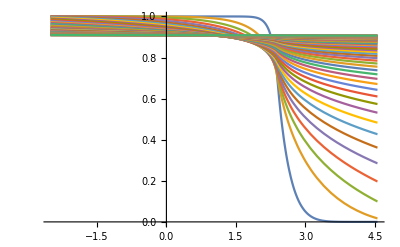

```mathematica
(* Plotting diffusion evolution at each time step *)

Plot[Evaluate[Table[p[t,x]/.solbud,{t,.1,30,0.5}]],{x,-rMnum,xfnum},PlotRange->All]
```

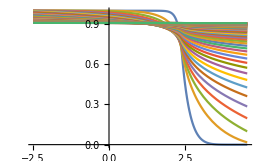

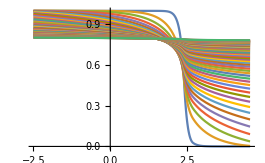

```mathematica
Plot[Evaluate[Table[p[t,x]/.solbudnonuni,{t,.1,30,0.5}]],{x,-rMnum,xfnum},PlotRange->All]
```

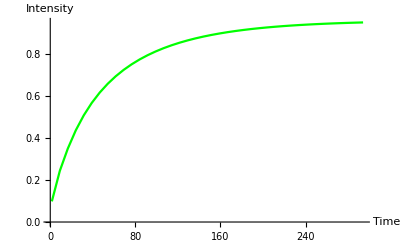

```mathematica
(* Evaluating and plotting normalized intensity *)

gbudtape=ListPlot[Table[{15t,(lengthtotal/lengthbud)*(1/(NIntegrate[(1/Sqrt[cm[x]])p[t,x]/.solbud,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])p[t,x]/.solbud,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[1/Sqrt[cd[x]]p[t,x]/.solbud,{x,xinitnumbud,xfnum},MaxRecursion->10][[1]]},{t,.1,20,0.5}],Joined  ->True,PlotStyle->Green,PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

```mathematica
numbudtape=Table[{15t,(lengthtotal/lengthbud)*(1/(NIntegrate[(1/Sqrt[cm[x]])p[t,x]/.solbud,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])p[t,x]/.solbud,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[1/Sqrt[cd[x]]p[t,x]/.solbud,{x,xinitnumbud,xfnum},MaxRecursion->10][[1]]},{t,.1,20,0.5}]
```

{{1.5,0.102366},{9.,0.253781},{16.5,0.364107},{24.,0.454748},{31.5,0.529047},{39.,0.590516},{46.5,0.641945},{54.,0.685424},{61.5,0.722531},{69.,0.754434},{76.5,0.782048},{84.,0.806087},{91.5,0.827115},{99.,0.845597},{106.5,0.861896},{114.,0.876304},{121.5,0.889071},{129.,0.900413},{136.5,0.910515},{144.,0.919529},{151.5,0.927584},{159.,0.934792},{166.5,0.941251},{174.,0.947045},{181.5,0.952248},{189.,0.956924},{196.5,0.961129},{204.,0.964914},{211.5,0.968322},{219.,0.971393},{226.5,0.974161},{234.,0.976657},{241.5,0.978909},{249.,0.98094},{256.5,0.982775},{264.,0.98443},{271.5,0.985926},{279.,0.987277},{286.5,0.988497},{294.,0.989599}}

```mathematica
Export["C:/transport/Trimble bud diffusion/bud-numbers-2017-list",numbudtape,"Table"]
```

C:/transport/Trimble bud diffusion/bud-numbers-2017-list

```mathematica
Export["C:/transport/Trimble bud diffusion/bud-low-D-numbers-2017-list",numbudtapenonuni,"Table"]
```

C:/transport/Trimble bud diffusion/bud-low-D-numbers-2017-list

```mathematica
numbudtapenonuni=Table[{15t,(lengthtotal/lengthbud)*(1/(NIntegrate[(1/Sqrt[cm[x]])p[t,x]/.solbudnonuni,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])p[t,x]/.solbudnonuni,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[1/Sqrt[cd[x]]p[t,x]/.solbudnonuni,{x,xinitnumbud,xfnum},MaxRecursion->10][[1]]},{t,.1,20,0.5}];
```

```mathematica
numbudtapenonuni
```

{{1.5,0.0151782},{9.,0.0392636},{16.5,0.0686284},{24.,0.10067},{31.5,0.133008},{39.,0.164511},{46.5,0.194771},{54.,0.223688},{61.5,0.251307},{69.,0.277713},{76.5,0.303003},{84.,0.327272},{91.5,0.350606},{99.,0.373074},{106.5,0.394738},{114.,0.415647},{121.5,0.435845},{129.,0.455368},{136.5,0.474247},{144.,0.49251},{151.5,0.51018},{159.,0.52728},{166.5,0.543828},{174.,0.559843},{181.5,0.57534},{189.,0.590336},{196.5,0.604845},{204.,0.618882},{211.5,0.632458},{219.,0.645589},{226.5,0.658285},{234.,0.67056},{241.5,0.682426},{249.,0.693894},{256.5,0.704975},{264.,0.715681},{271.5,0.726023},{279.,0.736011},{286.5,0.745657},{294.,0.75497}}

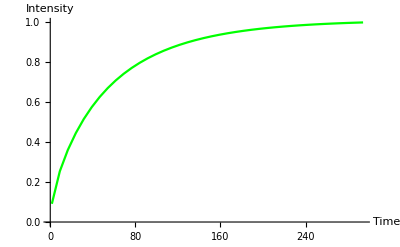

```mathematica
gbudarea=ListPlot[Table[{15t,(areatotal/areabud)*(1/(NIntegrate[(2Pi fm[x]/Sqrt[cm[x]])p[t,x]/.solbud,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(2Pi fd[x]/Sqrt[cd[x]])p[t,x]/.solbud,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[2Pi fd[x]/Sqrt[cd[x]]p[t,x]/.solbud,{x,xinitnumbud,xfnum},MaxRecursion->10][[1]]},{t,.1,20,0.5}],Joined  ->True,PlotStyle->Green,PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

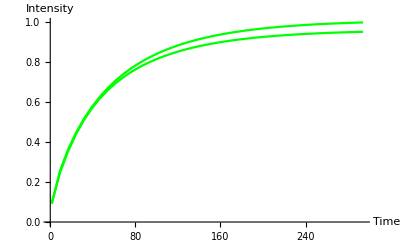

```mathematica
Show[gbudarea,gbudtape]
```

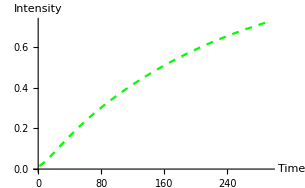

```mathematica
gbudtapenonuni=ListPlot[Table[{15t,(lengthtotal/lengthbud)*(1/(NIntegrate[(1/Sqrt[cm[x]])p[t,x]/.solbudnonuni,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])p[t,x]/.solbudnonuni,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[1/Sqrt[cd[x]]p[t,x]/.solbudnonuni,{x,xinitnumbud,xfnum},MaxRecursion->10][[1]]},{t,.1,20,0.5}],Joined  ->True,PlotStyle->{Green,Dashed},PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

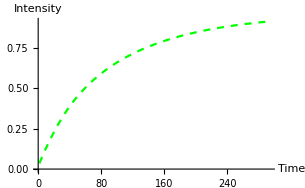

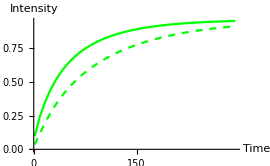

```mathematica
Show[gbudtape,gbudtapenonuni]
```

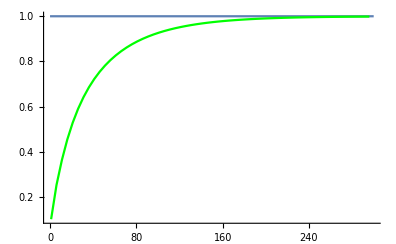

```mathematica
(* Checking normalization *)

Show[Plot[1,{x,0,300}],gbudtape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

### Solution: Big Cap

```mathematica
(* defining left-most x-coordinate for big cap region *)

xinitnumbig=-0.1;

(* defining big cap area & length *)

lengthbigcap = 2*NIntegrate[1/Sqrt[cm[x]], {x, -rMnum, xinitnumbig}]
areabigcap = 2*Pi*NIntegrate[fm[x]/Sqrt[cm[x]], {x, -rMnum, xinitnumbig}]
```

7.65393

37.6991

```mathematica
(* evaluating diffusion equation *)

solbig=NDSolve[{D[u[t,x], t]== Piecewise[{{cm[x],x<x0num},{cd[x],x>x0num}},cm[x]]D[u[t,x],x,x]+Piecewise[{{dm[x],x<x0num},{dd[x],x>x0num}},dm[x]]D[u[t,x],x]-0. u[t,x],u[0,x]==initcondition[x,xinitnumbig]},u,{t,0,40},{x,-rMnum,xfnum},MaxStepSize->0.5];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

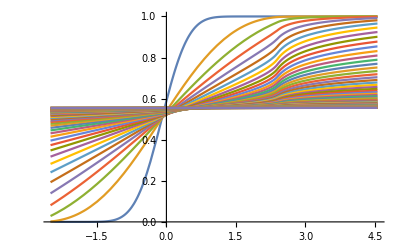

```mathematica
(* Plotting diffusion evolution at each time step *)

Plot[Evaluate[Table[u[t,x]/.solbig,{t,.1,40,0.5}]],{x,-rMnum,xfnum},PlotRange->All]
```

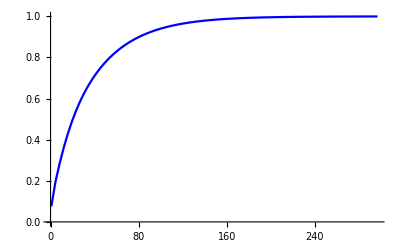

```mathematica
(* Evaluating and plotting normalized intensity *)

gbigtape=ListPlot[Table[{7.5t,(lengthtotal/lengthbigcap)*(1/(NIntegrate[(1/Sqrt[cm[x]])u[t,x]/.solbig,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])u[t,x]/.solbig,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[(1/Sqrt[cm[x]])u[t,x]/.solbig,{x,-rMnum, xinitnumbig},MaxRecursion->10][[1]]},{t,.1,40,0.5}],Joined->True,PlotStyle->Blue,PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

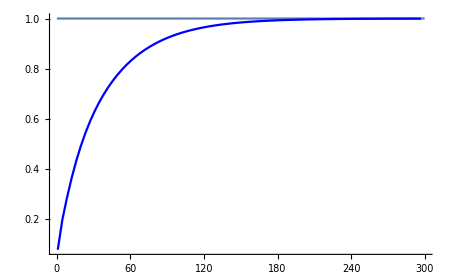

```mathematica
Show[Plot[1,{x,0,300}],gbigtape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

### Solution: Small Cap

```mathematica
(* defining left-most x-coordinate for small cap region *)

xinitnumsmall=-0.8;

(* defining small cap area & length *)

lengthsmallcap = 2*NIntegrate[1/Sqrt[cm[x]], {x, -rMnum,xinitnumsmall}]
areasmallcap= 2*Pi*NIntegrate[fm[x]/Sqrt[cm[x]], {x, -rMnum,xinitnumsmall}]
```

6.22533

26.7035

```mathematica
solsmall=NDSolve[{D[n[t,x], t]== Piecewise[{{cm[x],x<x0num},{cd[x],x>x0num}},cm[x]]D[n[t,x],x,x]+Piecewise[{{dm[x],x<x0num},{dd[x],x>x0num}},dm[x]]D[n[t,x],x]-0.n[t,x],n[0,x]==initcondition[x,xinitnumsmall]},n,{t,0,60},{x,-rMnum,xfnum},MaxStepSize->0.5];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

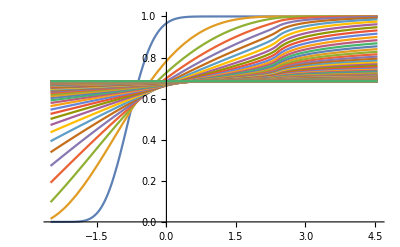

```mathematica
Plot[Evaluate[Table[n[t,x]/.solsmall,{t,.1,60,0.5}]],{x,-rMnum,xfnum},PlotRange->All]
```

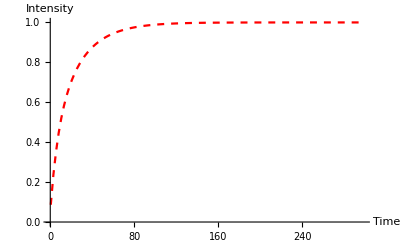

```mathematica
gsmalltape=ListPlot[Table[{5t,(lengthtotal/lengthsmallcap)*(1/(NIntegrate[(1/Sqrt[cm[x]])n[t,x]/.solsmall,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])n[t,x]/.solsmall,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[(1/Sqrt[cm[x]])n[t,x]/.solsmall,{x,-rMnum,xinitnumsmall},MaxRecursion->10][[1]]},{t,.1,60,0.5}],Joined->True,PlotRange->All, PlotStyle->{Red,Dashed}, AxesLabel->{"Time","Intensity"}]
```

```mathematica
1/15.
```

0.0666667

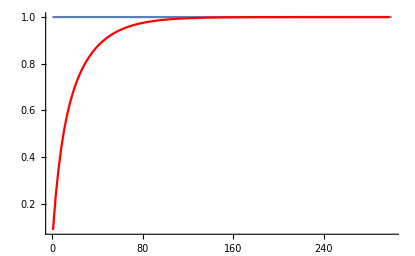

```mathematica
Show[Plot[1,{x,0,300}],gsmalltape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

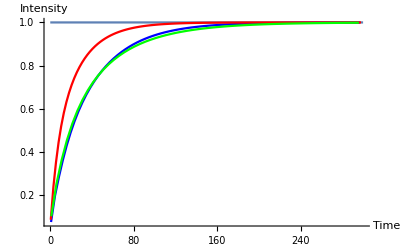

```mathematica
(* Plotting all theoretical normalized intensities together *)

Show[Plot[1,{x,0,300}],gbigtape,gsmalltape,gbudtape,PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

### Experimental Data

```mathematica
(* Defining time sequence, total of 305s *)

timeseq={0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305};
```

### Data: Full Normalised Intensity of Two Caps & Bud

```mathematica
(* Mean fluorescence intensity per pixel of bl area, as normalized by FRAP_Profiler*)
```

### Data: Bud

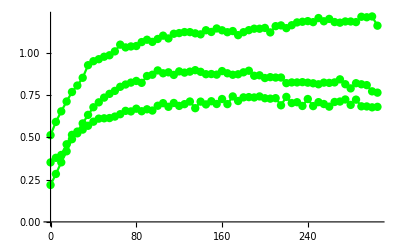

```mathematica
buds4555meanFRAPnorMnum=Import["C:\\Users\\Kat\\Documents\\Anton_Jess_Research\\data\\budsorignormalized_4.5_5.5_update.csv"];

Transpose[buds4555meanFRAPnorMnum];

b0014norMnumFRAP = Delete[Transpose[buds4555meanFRAPnorMnum][[1]], {{-2},{-1},{1},{2},{3},{4},{5}}];

b0023norMnumFRAP = Delete[Transpose[buds4555meanFRAPnorMnum][[2]], {{-2},{-1},{1},{2},{3},{4},{5}}];

b0034norMnumFRAP = Delete[Transpose[buds4555meanFRAPnorMnum][[3]], {{-2},{-1},{1},{2},{3},{4},{5}}];

buds4555meanFRAPnorMnumplot = ListLinePlot[{Transpose[{timeseq, b0014norMnumFRAP}],Transpose[{timeseq, b0023norMnumFRAP}],Transpose[{timeseq ,b0034norMnumFRAP}]}, Mesh -> All, PlotStyle-> Green, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

### Data: Small Cap

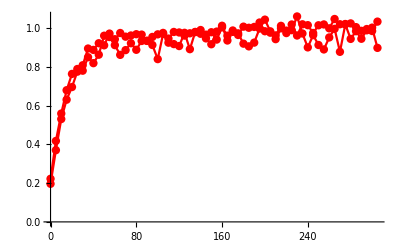

```mathematica
smcapFRAPnorMnum=Import["C:\\Users\\Kat\\Documents\\Anton_Jess_Research\\data\\smcaporignormalized.csv"];

Transpose[smcapFRAPnorMnum];

m002smnorMnumFRAP = Delete[Transpose[smcapFRAPnorMnum][[1]], {{1},{2},{3}}];

m009smnorMnumFRAP = Delete[Transpose[smcapFRAPnorMnum][[2]], {{1},{2},{3}}];

smcapmeanFRAPnorMnumplot=ListLinePlot[{Transpose[{timeseq,m002smnorMnumFRAP}],Transpose[{timeseq, m009smnorMnumFRAP}]}, Mesh->All, PlotStyle-> Red, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

### Data: Big Cap

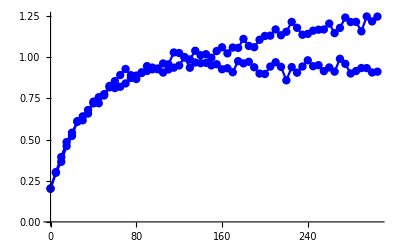

```mathematica
lrgcapFRAPnorMnum=Import["C:\\Users\\Kat\\Documents\\Anton_Jess_Research\\data\\lrgcaporignormalized.csv"];
Transpose[lrgcapFRAPnorMnum];

msq004lrgnorMnumFRAP = Delete[Transpose[lrgcapFRAPnorMnum][[1]], {{1},{2},{3}}];
msq007lrgnorMnumFRAP = Delete[Transpose[lrgcapFRAPnorMnum][[2]], {{1},{2},{3}}];

lrgcapmeanFRAPnorMnumplot=ListLinePlot[{Transpose[{timeseq,msq004lrgnorMnumFRAP}],Transpose[{timeseq, msq007lrgnorMnumFRAP}]},Mesh->All, PlotStyle-> Blue, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

### Theory + Experiment

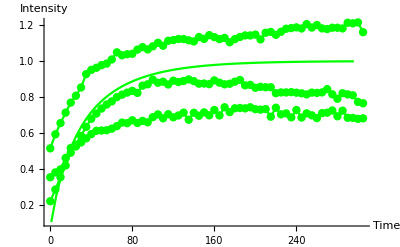

```mathematica
(* BUD *)

Show[buds4555meanFRAPnorMnumplot,gbudtape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

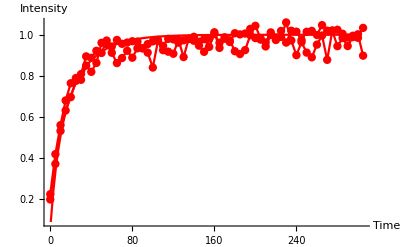

```mathematica
(* SMALL CAP *)

Show[smcapmeanFRAPnorMnumplot, gsmalltape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

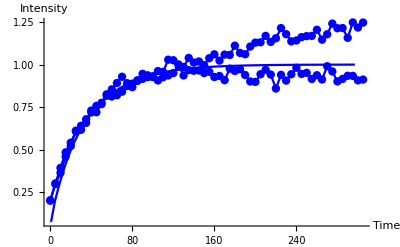

```mathematica
(* BIG CAP *)

Show[lrgcapmeanFRAPnorMnumplot,gbigtape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

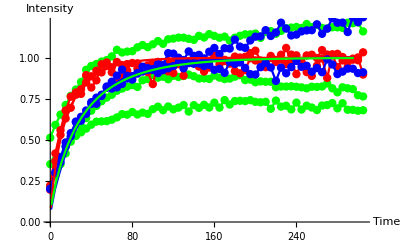

```mathematica
(* EVERYTHING *)

Show[buds4555meanFRAPnorMnumplot, smcapmeanFRAPnorMnumplot, lrgcapmeanFRAPnorMnumplot,gbigtape,gsmalltape,gbudtape, AxesLabel->{"Time","Intensity"}]
```

```mathematica
(70+101+86+90)0.1+0.1 90 +0.15 90
```

57.2

```mathematica
10.588 1.06
```

11.2233

```mathematica
11.2233+ 118.502
```

129.725

```mathematica
11.6468-1.635
```

10.0118

```mathematica
3^□
```

```mathematica
2600 0.17
```

442.

```mathematica
(* PARAMETERS FOR FINAL 2017 DATA *)
```

```mathematica
(*rMnum = radius of mother cell*)
(*rRnum = ratio of mother to daughter cell radii*)
(*x0num = bud neck location, where mother & daughter cells intersect*)
(*xfnum = right-most edge of bud*)

rMnum=2.5000000;
rRnum= 2.1000000;
rDnum = rMnum/rRnum;

x0num=2.4000000;
xfnum = x0num + rDnum + Sqrt[x0num^2 + rDnum^2 - rMnum^2];

Print[rMnum^2(1/rRnum^2-1)+x0num^2, " must be positive"]
```

0.927234 must be positive

Define the circles that characterize the spheres :

```mathematica
fm[x_]=Sqrt[rMnum^2-x^2];
fd[x_]=Sqrt[rDnum^2-(x-x0num-Sqrt[x0num^2+rDnum^2-rMnum^2])^2];
```

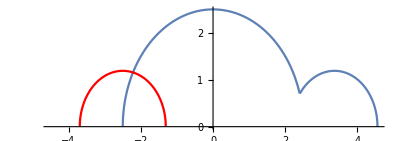

```mathematica
Show[Plot[Piecewise[{{fm[x],x<x0num},{fd[x],x>=x0num}}],{x,-rMnum-2,xfnum},AspectRatio->rMnum/(rMnum+xfnum)],Plot[Sqrt[(rMnum/rRnum)^2-(x+rMnum)^2],{x,-rMnum-2,xfnum},PlotStyle->Red]]
```

```mathematica
xc=x/.FindRoot[fm[x]==Sqrt[(rMnum/rRnum)^2-(x+rMnum)^2],{x,-2}]
```

-2.21655

```mathematica
(*geometry for equal cap-bud areas *)
```

```mathematica
(*bud area=17; cap area =2 Pi R h' h=17/(2 Pi R)*)
```

```mathematica
xc=-2.5+17.03/(2 Pi 2.5)
```

-1.41584

```mathematica
(* defining left-most x-coordinate for small cap region *)

xinitnumsmall=xc;

(* defining small cap area & length *)

lengthsmallcap = 2*NIntegrate[1/Sqrt[cm[x]], {x, -rMnum,xinitnumsmall}]
areasmallcap= 2*Pi*NIntegrate[fm[x]/Sqrt[cm[x]], {x, -rMnum,xinitnumsmall}]
```

2.40404

4.45237

```mathematica
solcap2017=NDSolve[{D[n[t,x], t]== Piecewise[{{cm[x],x<x0num},{cd[x],x≥ x0num}}]D[n[t,x],x,x]+Piecewise[{{dm[x],x<x0num},{dd[x],x≥ x0num}}]D[n[t,x],x]-0.n[t,x],n[0,x]==initcondition[x,xinitnumsmall]},n,{t,0,20},{x,-rMnum,xfnum},MaxStepSize->0.5];
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

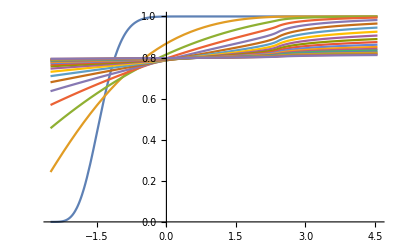

```mathematica
Plot[Evaluate[Table[n[t,x]/.solcap2017,{t,.1,20,1}]],{x,-rMnum,xfnum},PlotRange->All]
```

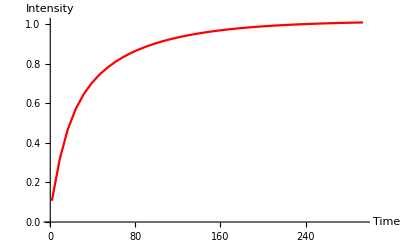

```mathematica
gcaptape2017=ListPlot[Table[{15t,(lengthtotal/lengthsmallcap)*(1/(NIntegrate[(1/Sqrt[cm[x]])n[t,x]/.solcap2017,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])n[t,x]/.solcap2017,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[(1/Sqrt[cm[x]])n[t,x]/.solcap2017,{x,-rMnum,xinitnumsmall},MaxRecursion->10][[1]]},{t,.1,20,0.5}],Joined->True,PlotRange->All, PlotStyle->Red, AxesLabel->{"Time","Intensity"}]
```

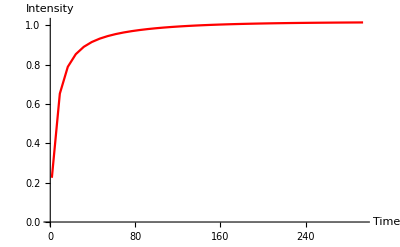

```mathematica
numcaptape2017=Table[{15t,(lengthtotal/lengthsmallcap)*(1/(NIntegrate[(1/Sqrt[cm[x]])n[t,x]/.solcap2017,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(1/Sqrt[cd[x]])n[t,x]/.solcap2017,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[(1/Sqrt[cm[x]])n[t,x]/.solcap2017,{x,-rMnum,xinitnumsmall},MaxRecursion->10][[1]]},{t,.1,20,0.5}]
```

{{1.5,0.221192},{9.,0.642124},{16.5,0.77615},{24.,0.839347},{31.5,0.875975},{39.,0.899999},{46.5,0.917019},{54.,0.929771},{61.5,0.939788},{69.,0.947827},{76.5,0.954451},{84.,0.960011},{91.5,0.964739},{99.,0.968797},{106.5,0.972304},{114.,0.975355},{121.5,0.978021},{129.,0.980364},{136.5,0.982428},{144.,0.984255},{151.5,0.985874},{159.,0.987314},{166.5,0.988597},{174.,0.989742},{181.5,0.990766},{189.,0.991682},{196.5,0.992504},{204.,0.993241},{211.5,0.993903},{219.,0.994498},{226.5,0.995034},{234.,0.995516},{241.5,0.995951},{249.,0.996342},{256.5,0.996696},{264.,0.997014},{271.5,0.997302},{279.,0.997561},{286.5,0.997795},{294.,0.998007}}

```mathematica
Export["C:/transport/Trimble bud diffusion/cap-numbers-2017-list",numcaptape2017,"Table"]
```

C:/transport/Trimble bud diffusion/cap-numbers-2017-list

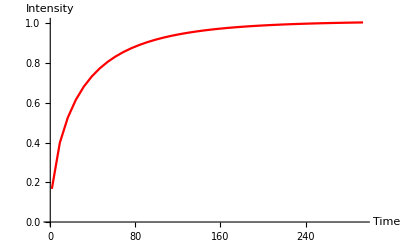

```mathematica
gcaparea2017=ListPlot[Table[{15t,(areatotal/areasmallcap)*(1/(NIntegrate[(fm[x]/Sqrt[cm[x]])n[t,x]/.solcap2017,{x,-rMnum,x0num},MaxRecursion->10][[1]]+NIntegrate[(fd[x]/Sqrt[cd[x]])n[t,x]/.solcap2017,{x,x0num,xfnum},MaxRecursion->10][[1]]))*NIntegrate[(fm[x]/Sqrt[cm[x]])n[t,x]/.solcap2017,{x,-rMnum,xinitnumsmall},MaxRecursion->10][[1]]},{t,.1,20,0.5}],Joined->True,PlotRange->All, PlotStyle->Red, AxesLabel->{"Time","Intensity"}]
```

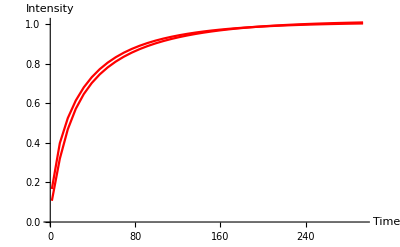

```mathematica
Show[gcaptape2017,gcaparea2017]
```

```mathematica
Show[Plot[1,{x,0,300}],gsmalltape, PlotRange->All, AxesLabel->{"Time","Intensity"}]
```

-Graphics-

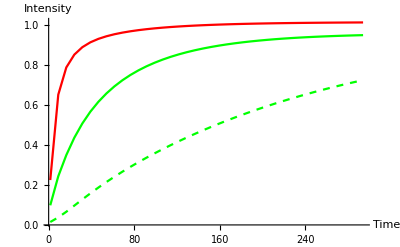

```mathematica
Show[gcaptape2017,gbudtape,gbudtapenonuni,PlotRange->All]
```

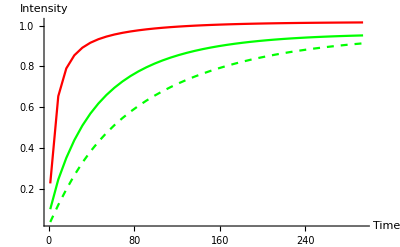

```mathematica
(*cap and bud of equalareas *)
```

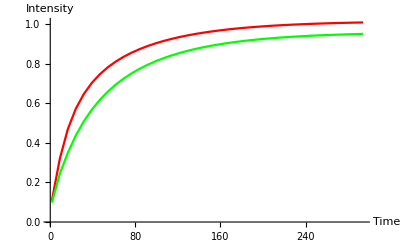

```mathematica
Show[gcaptape2017,gbudtape]
```

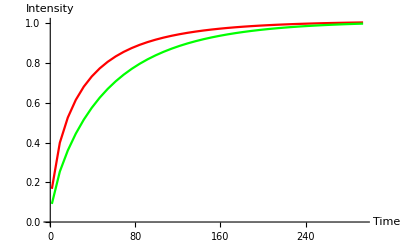

```mathematica
Show[gcaparea2017,gbudarea]
```